## 6144513020 - Doesn’t Concatenate

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
6144513020:{"AAB"->"BAA","A"->"B","B"->"AA"}
```

```mathematica
rs01=FromReducedRankIndex[6144513020]
```

<|Index→6144513020,QCode→33424332242423,RuleSet→{AAB→BAA,A→B,B→AA}|>

```mathematica
rs01[["RuleSet"]]
```

{AAB→BAA,A→B,B→AA}


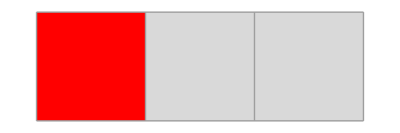

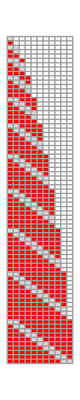
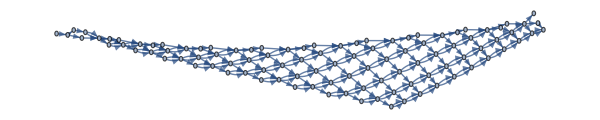
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss01=SSS[rs01[["RuleSet"]], "A",500,
 SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

```mathematica
sss01[["Net"]]//Short
```

{1→2,2→3,2→4,3→5,5→6,5→6,4→6,6→7,6→8,6→9,9→10,«1299»,496→497,467→497,497→498,497→498,468→498,498→499,498→499,469→499,499→500,499→500,470→500}

```mathematica
nds01=ToNetDifferenceSets[sss01[["Net"]]]
```

{{1},{1,2},{2},{2},{1,1},{1,2,3},{3},{3},{1,1},{1,1,4},{1,2,4},{4},{4},{1,1},{1,1,5},{1,1,5},{1,2,5},{5},{5},{1,1},{1,1,6},{1,1,6},{1,1,6},{1,2,6},{6},{6},{1,1},{1,1,7},{1,1,7},{1,1,7},{1,1,7},{1,2,7},{7},{7},{1,1},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{1,2,8},{8},{8},{1,1},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,2,9},{9},{9},{1,1},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,2,10},{10},{10},{1,1},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,2,11},{11},{11},{1,1},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,2,12},{12},{12},{1,1},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,2,13},{13},{13},{1,1},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,2,14},{14},{14},{1,1},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,2,15},{15},{15},{1,1},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,2,16},{16},{16},{1,1},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,2,17},{17},{17},{1,1},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,1,18},{1,2,18},{18},{18},{1,1},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,2,19},{19},{19},{1,1},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,1,20},{1,2,20},{20},{20},{1,1},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,2,21},{21},{21},{1,1},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,1,22},{1,2,22},{22},{22},{1,1},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,2,23},{23},{23},{1,1},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,1,24},{1,2,24},{24},{24},{1,1},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,2,25},{25},{25},{1,1},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,1,26},{1,2,26},{26},{26},{1,1},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,1,27},{1,2,27},{27},{27},{1,1},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,1,28},{1,2,28},{28},{28},{1,1},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,1,29},{1,2,29},{29},{29},{1,1},{1,1,30},{1,1,30},{1,1,30},{1,1,30},{1,1,30},{1,1,30},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,2},{},{},{1,1},{1,1},{1,1},{1,1},{1,1}}

```mathematica
Position[nds01,{29}]
```

{{462},{463}}

```mathematica
rsl01=ReduceSetList[nds01[[1;;463]]]
```

{{1},{1,2},€_(n$1⊨1)^27[€^2[{1+n$1}],{1,1},€^(-1+n$1)[{1,1,2+n$1}],{1,2,2+n$1}],€^2[{29}]}

```mathematica
ans=(rsl01[[3;;3]]/.n$1->k)
```

{€_(k⊨1)^27[€^2[{1+k}],{1,1},€^(-1+k)[{1,1,2+k}],{1,2,2+k}]}

```mathematica
ans//InputForm
```

{IndexedConcatenate[IndexedConcatenate[{1 + k}, 2], {1, 1}, IndexedConcatenate[{1, 1, 2 + k}, -1 + k], {1, 2, 2 + k}, {k, 1, 27}]}

```mathematica
{IndexedConcatenate[IndexedConcatenate[{1 + k}, 2], {1, 1}, IndexedConcatenate[{1, 1, 2 + k}, -1 + k], {1, 2, 2 + k}, {k, 0,1}]}//Expand
```

{{1},{1},{1,1},€^-1[{1,1,2}],{1,2,2},{2},{2},{1,1},€^0[{1,1,3}],{1,2,3}}

```mathematica
{IndexedConcatenate[IndexedConcatenate[{1 + k}, 2], {1, 1}, IndexedConcatenate[{1, 1, 2 + k}, -1 + k], {1, 2, 2 + k}, {k, 0,27}]}
```

{€_(k⊨0)^27[€^2[{k+1}],{1,1},€^(k-1)[{1,1,k+2}],{1,2,k+2}]}

```mathematica
{IndexedConcatenate[IndexedConcatenate[{k}, 2], {1, 1}, IndexedConcatenate[{1, 1, 1+ k}, -2 + k], {1, 2, 1 + k}, {k, 1,27}]}
```

{€_(k⊨1)^27[€^2[{k}],{1,1},€^(k-2)[{1,1,k+1}],{1,2,k+1}]}